Set::write: Null\ {{0, 10}, {-10/√3, 0}, {10/√3, 0}, {0, 10}} 中的标签 Times 被保护.

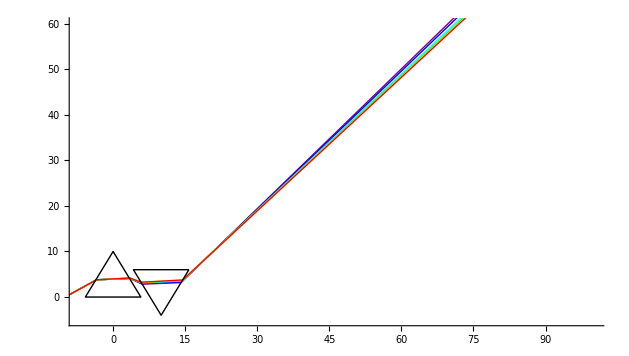

```mathematica
hx[ϕ_]:=(data={{4046.6,1.806},{4339.2,1.793},{4916.0,1.774},{5460.7,1.762},{5893.0,1.756},{6562.8,1.753}};
n=Transpose[data];n=n[[2]];c={Purple,Blue,Cyan,Green,Yellow,Red};
n1=n3=n5=1.0;h2=10;h1=0;h3=-4;d=10;θ=π/6;
γ=π/6;α=π/3;
optics={};x1=-10;x2=100;
Do[n2=n4=n[[i]];
k=n1{Cos[γ],Sin[γ]};p1={x1,h1};
equ={k[[1]](y-p1[[2]])==k[[2]](x-p1[[1]]),y-((10/3+20/3 Sin[ϕ])-(10/3+20/3 Sin[ϕ+(2π)/3]))/((20/3 Cos[ϕ])-(20/3 Cos[ϕ+(2π)/3]))(x-20/3 Cos[ϕ])-(10/3+20/3 Sin[ϕ])==0};
s=NSolve[equ,{x,y}];
p2={x,y}/.s[[1]];
f=-y+((10/3+20/3 Sin[ϕ])-(10/3+20/3 Sin[ϕ+(2π)/3]))/((20/3 Cos[ϕ])-(20/3 Cos[ϕ+(2π)/3]))(x-20/3 Cos[ϕ])+(10/3+20/3 Sin[ϕ]);
ω=D[f,{{x,y}}]/.Thread[{x,y}->p2];
ω=ω/Norm[ω];G1=k.ω;G2=Sqrt[n2^2-n1^2+G1^2];
k=k+(G2-G1)ω;
equ={k[[1]](y-p2[[2]])==k[[2]](x-p2[[1]]),y-((10/3+20/3 Sin[ϕ])-(10/3+20/3 Sin[ϕ+(4π)/3]))/((20/3 Cos[ϕ])-(20/3 Cos[ϕ+(4π)/3]))(x-20/3 Cos[ϕ])-(10/3+20/3 Sin[ϕ])==0};
s=NSolve[equ,{x,y}];
p3={x,y}/.s[[1]];
f=y+Cot[α/2]x-h2;
ω=D[f,{{x,y}}]/.Thread[{x,y}->p3];
ω=ω/Norm[ω];G1=k.ω;G2=Sqrt[n3^2-n2^2+G1^2];
k=k+(G2-G1)ω;
equ={k[[1]](y-p3[[2]])==k[[2]](x-p3[[1]]),y-((8/3+20/3 Sin[θ+(2π)/3])-(8/3+20/3 Sin[θ+(4π)/3]))/((10+20/3 Cos[θ+(2π)/3])-(10+20/3 Cos[θ+(4π)/3]))(x-10-20/3 Cos[θ+(2π)/3])-(8/3+20/3 Sin[θ+(2π)/3])==0};
s=NSolve[equ,{x,y}];
p4={x,y}/.s[[1]];
f=y-((8/3+20/3 Sin[θ+(2π)/3])-(8/3+20/3 Sin[θ+(4π)/3]))/((10+20/3 Cos[θ+(2π)/3])-(10+20/3 Cos[θ+(4π)/3]))(x-10-20/3 Cos[θ+(2π)/3])-(8/3+20/3 Sin[θ+(2π)/3]);
ω=D[f,{{x,y}}]/.Thread[{x,y}->p4];
ω=ω/Norm[ω];G1=k.ω;G2=Sqrt[n4^2-n3^2+G1^2];
k=k+(G2-G1)ω;
equ={k[[1]](y-p4[[2]])==k[[2]](x-p4[[1]]),-y+((8/3+20/3 Sin[θ])-(8/3+20/3 Sin[θ+(4π)/3]))/((10+20/3 Cos[θ])-(10+20/3 Cos[θ+(4π)/3])) (x-10-20/3 Cos[θ])+(8/3+20/3 Sin[θ])==0};
s=NSolve[equ,{x,y}];
p5={x,y}/.s[[1]];
f=-y+((8/3+20/3 Sin[θ])-(8/3+20/3 Sin[θ+(4π)/3]))/((10+20/3 Cos[θ])-(10+20/3 Cos[θ+(4π)/3]))(x-10-20/3 Cos[θ])-(8/3+20/3 Sin[θ]);
ω=D[f,{{x,y}}]/.Thread[{x,y}->p5];
ω=ω/Norm[ω];G1=k.ω;G2=Sqrt[n5^2-n4^2+G1^2];
k=k+(G2-G1)ω;
p6={x,k[[2]]/k[[1]] (x-p5[[1]])+p5[[2]]}/.x->x2;
line1={p1,p2,p3,p4,p5,p6};
AppendTo[optics,Graphics[{c[[i]],Line[line1]}]],{i,Length[n]}]

line2={{20/3 Cos[π/2],10/3+20/3 Sin[π/2]},{20/3 Cos[π/2+(2π)/3],10/3+20/3 Sin[π/2+(2π)/3]},{20/3 Cos[π/2+(4π)/3],10/3+20/3 Sin[π/2+(4π)/3]},{20/3 Cos[π/2],10/3+20/3 Sin[π/2]}};
line3={{10+20/3 Cos[θ],8/3+20/3 Sin[θ]},{10+20/3 Cos[θ+(2π)/3],8/3+20/3 Sin[θ+(2π)/3]},
{10+20/3 Cos[θ+(4π)/3],8/3+20/3 Sin[θ+(4π)/3]},{10+20/3 Cos[θ],8/3+20/3 Sin[θ]}};
Show[optics,Graphics[{Thick,Line/@{line2,line3}},Axes->True],AspectRatio->Automatic,Axes->True,PlotRange->{{-7,100},{-5,60}}]);
hx[π/2+0.1]
```

```mathematica
|
```

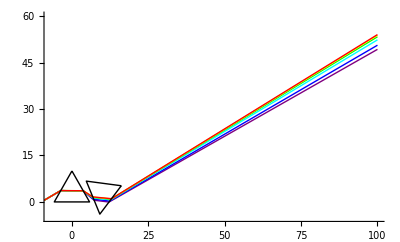
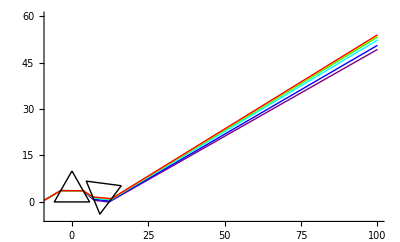
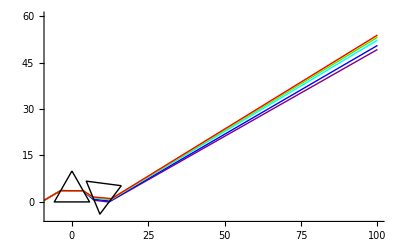
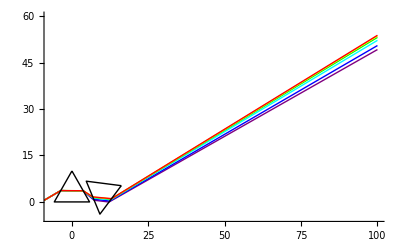
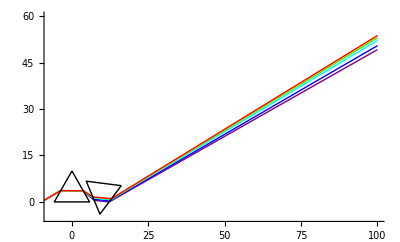
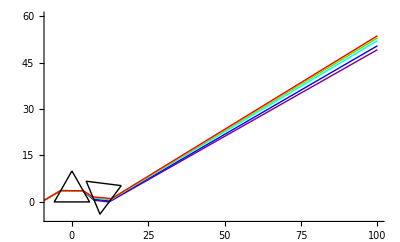
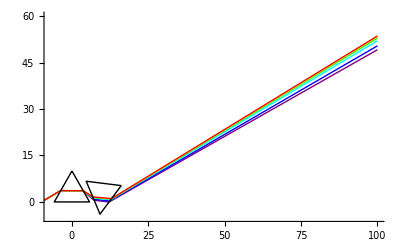
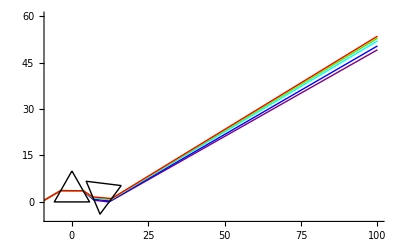
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
b=Table[gx[θ],{θ,π/8+0.001,(5π)/24+0.001,π/2400}];
Export["Animate"]
```

```mathematica
gx[π/8]
```

-Graphics-